### Naloga 1

```mathematica
GG=9.81;
H=10;
v0={10, 3};
x0={0, H};
a0={0, -GG};
X[t_]:=x0+v0 t+a0 t^2/2
```

```mathematica
X[t]
```

{10 t,10+3 t-4.905 t^2}

```mathematica
{10 t,10+3 t-4.905 t^2}
```

{10 t,10+3 t-4.905 t^2}

```mathematica
SlikaTocke[t_]:={PointSize[0.03], Point[X[t]]}
```

```mathematica
Graphics@SlikaTocke[1]
```

-Graphics-

```mathematica
SlikaTocke[1]
```

{PointSize[0.03],Point[{10,8.095}]}

```mathematica
V[t_]:=D[X[tt], tt]/.tt->t
```

```mathematica
V[1]
```

{10,-6.81}

```mathematica
V[t_]:=v0 +a0 t
V[t]
```

{10,3-9.81 t}

```mathematica
SlikaVektorja[t_,k_]:={Thickness[0.005], Arrow[{X[t], X[t] + V[t]*k}]}
```

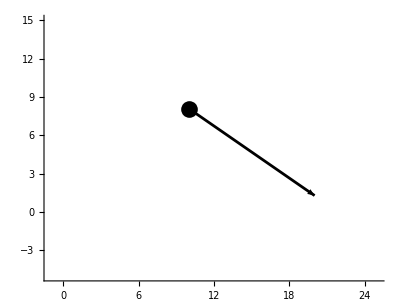

```mathematica
Graphics[{SlikaVektorja[1, 1], SlikaTocke[1]}, PlotRange-> {{-1, 25},{-5, 15}}, Axes->True, AspectRatio->Automatic]
```

```mathematica
?*Size
```

```mathematica
Slika[t_]:=Graphics[{SlikaVektorja[t,1], SlikaTocke[t]}, PlotRange-> {{-1, 25},{-5, 15}}, Axes->True, AspectRatio->Automatic]
```

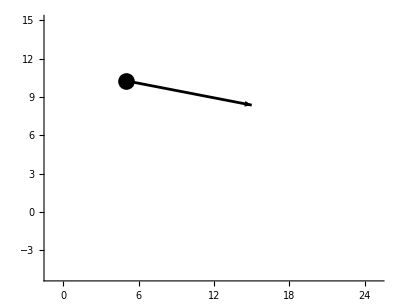

```mathematica
Slika[0.5]
```

```mathematica
Manipulate[Slika[t], {t, 0,5}]
```

```mathematica
?Slika
```

```mathematica
ClearAll[Slika]
```

```mathematica
casPristanka=t/.Solve[X[t][[2]]==0&&t>0, t]//First
```

1.76604

```mathematica
dolzinaPristanka=X[casPristanka]//First
```

17.6604

```mathematica
casMaxVisine=t/.Solve[D[X[t][[2]], t]==0, t]//First
```

0.30581

```mathematica
maxVisina=X[casMaxVisine][[2]]
```

10.4587

```mathematica
ClearAll[Slika]
```

```mathematica
Slika[t_]:=Graphics[{SlikaVektorja[t,0.5], SlikaTocke[t]}, PlotRange-> {{-1, dolzinaPristanka+5},{-5, maxVisina+1}}, Axes->True, AspectRatio->Automatic]
```

```mathematica
Manipulate[Slika[t], {t, 0,casPristanka}]
```

```mathematica
V[casPristanka]//Norm
```

17.47

```mathematica
V[casMaxVisine]
```

{10.,0.}

### Naloga 2

```mathematica
r111=Ravnina[{-1,-1,-1},{1,1,1}]
```

Ravnina[{-1,-1,-1},{1,1,1}]

```mathematica
Slika[Ravnina[n_, v_]]:=Hyperplane[n, v]
```

```mathematica
Slika[r111]
```

Hyperplane[{-1,-1,-1},{1,1,1}]

```mathematica
Graphics3D[Slika[r111]]
```

-Graphics3D-

```mathematica
Normala[Ravnina[n_, v_]]:=n
```

```mathematica
Tocka[Ravnina[n_, v_]]:=v
```

```mathematica
rx=Ravnina[{1, 0, 0}, {0, 0, 0}]
```

Ravnina[{1,0,0},{0,0,0}]

```mathematica
ry=Ravnina[{0, 1, 0}, {0, 0, 0}]
```

Ravnina[{0,1,0},{0,0,0}]

```mathematica
rz=Ravnina[{0, 0, 1}, {0, 0, 0}]
```

Ravnina[{0,0,1},{0,0,0}]

```mathematica
Graphics3D@Map[Slika,{r111, rx, ry, rz}]
```

-Graphics3D-

```mathematica
SlikaNormale[Ravnina[n_, v_]]:=Arrow[{v, v+n}]
```

```mathematica
SlikaNormale[r111]
```

Arrow[{{1,1,1},{0,0,0}}]

```mathematica
Graphics3D[{Slika[r111], SlikaNormale[r111]}, PlotRange-> {{-2,2},{-2,2},{-2,2}}, Axes->True, AxesOrigin->{0, 0, 0}]
```

-Graphics3D-

```mathematica
Enacba[Ravnina[n_, v_]]:=n.({x, y, z}-v)==0
```

```mathematica
Enacba[rx]
```

x==0

```mathematica
ResiSistem[sistem_List]:= Solve [sistem, {x, y, z}]
```

```mathematica
Ravnina[r111, rx, ry, rz]
```

Ravnina[Ravnina[{-1,-1,-1},{1,1,1}],Ravnina[{1,0,0},{0,0,0}],Ravnina[{0,1,0},{0,0,0}],Ravnina[{0,0,1},{0,0,0}]]

```mathematica
ravnine{r111, rx, ry, rz}
```

{ravnine Ravnina[{-1,-1,-1},{1,1,1}],ravnine Ravnina[{1,0,0},{0,0,0}],ravnine Ravnina[{0,1,0},{0,0,0}],ravnine Ravnina[{0,0,1},{0,0,0}]}

```mathematica
resitveDvojno={x, y, z}/. Map[ResiSistem,Subsets[Map[Enacba, {r111, rx, ry, rz}], {3}]]
```

{{{0,0,3}},{{0,3,0}},{{3,0,0}},{{0,0,0}}}

```mathematica
tocke=Map[First, resitveDvojno]
```

{{0,0,3},{0,3,0},{3,0,0},{0,0,0}}

```mathematica
Presecisca[ravnine_List]:= 
Map[First,
{x, y, z}/. Map[ResiSistem,Subsets[Map[Enacba, {r111, rx, ry, rz}], {3}]]]
```

```mathematica
Presecisca[ravnine]
```

Presecisca[ravnine]

```mathematica
Vsebuje[Ravnina[n_, v_], {x_, y_, z_}, eps_]:=
Abs[n.({x, y, z}-v)]< eps
```

```mathematica
r111
```

Ravnina[{-1,-1,-1},{1,1,1}]

```mathematica
Vsebuje[r111, {0, 0, 3}, 0.000001 ]
```

True

```mathematica
tocke={{0, 0, 3}, {1, 2, 3}, {-3, 4, 5}, {1, 1, 1}, {3, 0, 0}}
```

{{0,0,3},{1,2,3},{-3,4,5},{1,1,1},{3,0,0}}

```mathematica
vsebuje111[t_]:=Vsebuje[r111, t, 0.0000001]
```

```mathematica
Map[vsebuje111, tocke]
```

{True,False,False,True,True}

```mathematica
?Select
```

```mathematica
Select[{1, 2, 3,4,5},EvenQ]
```

{2,4}

```mathematica
EvenQ[3]
```

False

```mathematica
slikeTock=Map[Ball, tocke]
```

{Ball[{0,0,3}],Ball[{1,2,3}],Ball[{-3,4,5}],Ball[{1,1,1}],Ball[{3,0,0}]}

```mathematica
trikotnik=Polygon[Select[tocke, vsebuje111]]
```

Polygon[…]

```mathematica
zogice[t_]:=Ball[t,0.3]
```

```mathematica
slikeTock=Map[zogice, Select[tocke, vsebuje]]
```

{}

```mathematica
int=6
```

6

```mathematica
Graphics3D[{trikotnik, Slika[r111], slikeTock},
PlotRange->{{-int,int}, {-int,int}, {-int,int}}]
```

-Graphics3D-

```mathematica
SlikaTrikotnikovInZogic[ravnina_, tocke_]:=Module[{vsebuje,trikotnik, int, zogice, slikeTock},
vsebuje[t_]:=Vsebuje[ravnina, t, 0.0000001];
trikotnik=Polygon[Select[tocke, vsebuje]];
zogice[t_]:=Ball[t,0.3];
slikeTock=Map[zogice, Select[tocke, vsebuje]];
int=6;
Graphics3D[{trikotnik, Slika[ravnina], slikeTock},
PlotRange->{{-int,int}, {-int,int}, {-int,int}}]
]
```

```mathematica
SlikaTrikotnikovInZogic[r111, tocke]
```

-Graphics3D-

### Naloga 3

```mathematica
t000={0,0,0};
t001={0,0,1};
t010={0,1,0};
t011={0,1,1};
t100={1,0,0};
t101={1,0,1};
t110={1,1,0};
t111={1,1,1};
```

```mathematica
p1=Polygon[{t000, t001, t011, t010}]
p2=Polygon[{t100, t101, t111, t110}]
p3=Polygon[{t000, t010, t110, t100}]
p4=Polygon[{t111, t011, t001, t101}]
p5=Polygon[{t010, t110, t111, t011}]
p6=Polygon[{t000, t100, t101, t001}]
```

Polygon[…]

Polygon[…]

Polygon[…]

«3 more identical outputs»

```mathematica
Graphics3D[{p1, p2, p3, p4, p5, p6}, PlotRange-> {{-2,2},{-2,2},{-2,2}}, Axes->True]
```

-Graphics3D-